## Strang Splitting for NLS

Code is for 
	ⅈ u_t+1/2 u_xx+|u|^2 u=0

```mathematica
(*Parameters*)
L=10;(*Domain length*)
tmax=20;(*Time*)
kappa=1;(*Nonlinearity coefficient*)
(*NLS Equation:i*u_t+0.5 u_xx+kappa*|u|^2*u=0*)eq=I*D[u[x,t],t]+1/2 D[u[x,t],{x,2}]+kappa*Abs[u[x,t]]^2*u[x,t]==0;
(*Initial Condition (Soliton)*)
ic=u[x,0]==Sech[x];
(*Boundary Conditions (Periodic)*)
bc=u[-L,t]==u[L,t];
(*NDSolve*)
sol=NDSolveValue[{eq,ic,bc},u,{x,-L,L},{t,0,tmax}];
(*Plot Result*)
TabView[{
Plot3D[Abs[sol[x,t]],{x,-L,L},{t,0,tmax},PlotRange->All,
PlotPoints->100],
ContourPlot[Abs[sol[x,t]],{x,-L,L},{t,0,tmax},PlotRange->All,
PlotPoints->100,
GridLines->Automatic]},
2]
```

12

```mathematica
Clear[Sol,f,x,IC,u,t]
Sol[{η_,v_,x0_}][x_]:=η Sech[η (x-x0)/√2] Exp[I (v/2) (x-x0)]
{η1,v1,x1}={1,2,0};
f[x_]:= Sol[{η1,v1,x1}][x]
L=10; TMax=0.1;
uSol=NDSolveValue[ {
ⅈ D[u[x,t],t]+1/2 D[u[x,t],x,x]+Abs[u[x,t]]^2 u[x,t]==0,
u[x,0]==f[x],
u[-L,t]==u[L,t]
} ,
u,
{x,-L,L},
{t,0 ,TMax}]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
Options[NDSolveValue]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,DiscreteVariables→{},EvaluationMonitor→None,InitialSeeding→{},InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→Automatic,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

Splitting 
	ⅈ u_t=-1/2 u_xx
	ⅈ u_t=-|u|^2 u

```mathematica
NLSStep[dt_,LPhase_][uIn_]:=Module[
{uHalf},
(* Convert to Fourier Space advance by Δt/2 using LPhase *)
(* Check LPhase (computed externally)corresponds to dt/2 *)
uHalf=Fourier[uIn,FourierParameters->{1,-1}]*LPhase;
(* Convert back to Physical Space and advance by a full dt *)
uHalf=InverseFourier[uHalf,FourierParameters->{1,-1}];
uHalf=uHalf+dt Abs[uHalf]^2*uHalf;
(* Back to Fourier and complete linear advance by Δt/2 *)
uHalf=Fourier[uHalf,FourierParameters->{1,-1}]*LPhase;
(* back to physical sapce and return *)
InverseFourier[uHalf,FourierParameters->{1,-1}]
]
```

Testing

```mathematica
NDSolveValue[ 
i D[u[x,t],t]+
```

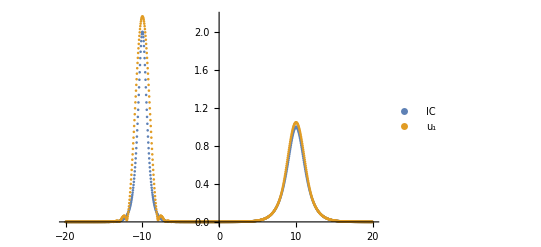

```mathematica
Clear[Sol,IC]
Sol[{η_,v_,x0_}][x_]:=η Sech[η (x-x0)] Exp[I (v/2) (x-x0)]
{L, Nx}={20.0,1000}; dx=(2.0L)/Nx;
{η1,v1,x1}={2,0,-10};
{η2,v2,x2}={1,0,10};
IC=Table[Sol[{η1,v1,x1}][x]+Sol[{η2,v2,x2}][x],{x, -L,L-dx,dx}];
ListPlot[Abs[IC],PlotRange->All,PlotLabel->"IC",DataRange->{-L,L}];
k=(Pi/L) Join[Range[0,Nx/2-1],Range[-Nx/2,-1]];
dt=0.01;
u=IC;
LPhase=Exp[-I  k^2 dt ];
Do[
u=NLSStep[dt,LPhase][u],
{10}];
ListPlot[{Abs[IC],Abs[u]},PlotRange->All,PlotLegends->{"IC","u_1"},DataRange->{-L,L}]
```

```mathematica
(*1. Parameters and Grid*)
L=50.0;(*Domain Size*)
n=256;(*Fourier Modes*)
dt=0.001;(*Time Step*)
tmax=10.0;(*Total Time*)
dx=L/n;
x=Table[-L/2+i*dx,{i,0,n-1}];

(*Initial Condition:Single Soliton*)
u=-0.5*Sech[0.5*(x-0)]^2;

(*2. Spectral Grid and Dispersion Linear Operator*)
k=Table[If[i<=n/2,i,i-n],{i,0,n-1}]*(2*Pi/L);

(*u_xxx=-i k^3 in spectral space*)
dispersion=Exp[-(I*k^3)*dt/2];

(*3. Split-Step Fourier Algorithm*)
steps=Round[tmax/dt];
Step[uIn_]:=Module[{uHat,uOut},
uHat=Fourier[u];
uHat=uHat*dispersion;
uOut=InverseFourier[uHat];

uHat=Fourier[uOut]
]
```

```mathematica
Do[
(*Step A:Half dispersion Step*)
uhat=Fourier[u];
uhat=uhat*dispersion;
u=InverseFourier[uhat];
(*Step B:Nonlinear Step (using 6 Subscript[uu, x]=3 Subscript[(u^2), x]*)
(*Using real space for quadratic non-linearity*)u=u-dt*(3*(RotateLeft[u]-RotateRight[u])/(2*dx)*2*u);
(*Simple nonlinear approximation:u=u-3dt u ux*)(*Step C:Half dispersion Step*)uhat=Fourier[u];
uhat=uhat*dispersion;
u=InverseFourier[uhat];
If[Mod[i,100]==0,AppendTo[solution,Re[u]]],{i,1,steps}];

(*4. Visualization*)
ListLinePlot[solution,PlotRange->All,ColorFunction->"TemperatureMap",Mesh->None,InterpolationOrder->2,PlotLabel->"KdV Soliton"]
```

Set::wrsym: Symbol N is Protected.

Table::iterb: Iterator {i,0,-1+N} does not have appropriate bounds.

Fourier::fftl: Argument -0.5 Sech[0.5 Table[«2» Power[«2»]+i dx,{i,0,-1+N}]]^2 is not a non-empty list or rectangular array of numeric quantities.

Table::iterb: Iterator {i,0,-1+N} does not have appropriate bounds.

InverseFourier::fftl: Argument ⅇ^((0.-9.92201×10^-7 ⅈ) Table[If[i≤Times[«2»],i,i+Times[«2»]],{i,0,-1+N}]^3) Fourier[-0.5 Sech[0.5 Table[Plus[«2»],{«3»}]]^2] is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument 0.+InverseFourier[ⅇ^((0.-9.92201×10^-7 ⅈ) Table[If[«3»],{«3»}]^3) Fourier[-0.5 Sech[Times[«2»]]^2]] is not a non-empty list or rectangular array of numeric quantities.

InverseFourier::fftl: Argument ⅇ^((0.-9.92201×10^-7 ⅈ) Table[If[i≤Times[«2»],i,i+Times[«2»]],{i,0,-1+N}]^3) Fourier[0.+InverseFourier[ⅇ^((0.-9.92201×10^-7 ⅈ) Power[«2»]) Fourier[-0.5 Power[«2»]]]] is not a non-empty list or rectangular array of numeric quantities.

Table::iterb: Iterator {i,0,-1+N} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Fourier::fftl: Argument -0.5 Sech[0.5 Table[«2» Power[«2»]+i dx,{i,0,-1+N}]]^2 is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

InverseFourier::fftl: Argument ⅇ^((0.-9.92201×10^-7 ⅈ) Table[If[i≤Times[«2»],i,i+Times[«2»]],{i,0,-1+N}]^3) Fourier[-0.5 Sech[0.5 Table[Plus[«2»],{«3»}]]^2] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of InverseFourier::fftl will be suppressed during this calculation.

# KdV Equation

```mathematica
Clear[x,t,u]
L=5;TMax=5;c=10;
uSol=NDSolveValue[{
D[u[x,t],t] + D[u[x,t],{x,3}]-6 u[x,t] D[u[x,t],x]==0,
u[x,0]==c/2 Sech[(√c)/2 x]^2,
u[-L,t]==u[L,t]
},
u,
{x, -L,L},
{t,0, TMax},
Method -> {
"PDEDiscretization" -> {"MethodOfLines", 
      "SpatialDiscretization" -> {"TensorProductGrid", "MaxPoints" -> 5000}}}]
```

NDSolveValue::mxsst: Using maximum number of grid points 5000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
Animate[Plot[uSol[x,t],{x, -L,L},
PlotRange->All,GridLines->Automatic],{t,0, TMax,0.1}]
```

## Try Again

```mathematica
Clear[x,t,u]
L=5;TMax=5;c=10;
uSol=NDSolveValue[{
D[u[x,t],t] + D[u[x,t],{x,3}]-6 u[x,t] D[u[x,t],x]==0,
u[x,0]==c/2 Sech[(√c)/2 x]^2,
u[-L,t]==u[L,t]
},
u,
{x, -L,L},
{t,0, TMax},
Method -> {
"PDEDiscretization" -> {"FiniteElement"}}]
```

NDSolveValue::femcmsd: The spatial derivative order of the PDE may not exceed two.

NDSolveValue[{u^(0,1)[x,t]-6 u[x,t] u^(1,0)[x,t]+u^(3,0)[x,t]==0,u[x,0]==5 Sech[√(5/2) x]^2,u[-5,t]==u[5,t]},u,{x,-5,5},{t,0,5},Method→{PDEDiscretization→{FiniteElement}}]

```mathematica
Animate[Plot[uSol[x,t],{x, -L,L},
PlotRange->All,GridLines->Automatic],{t,0, TMax,0.1}]
```